# SEI2HR model with quarantine scenarios

## Introduction

The epidemiology compartmental model, [Wk1], presented in this notebook -- SEI2HR -- deals with the left-most and middle rectangles in this diagram:

-Graphics-

“SEI2HR” stands for “Susceptible, Exposed, Infected two, Hospitalized, Recovered” (populations.)

In this notebook we also deal with quarantine scenarios.

Remark: We consider the contagious disease propagation models as instances of the more general System Dynamics (SD) models. We use SD terminology in this notebook.

### The models

#### SEI2R

The model SEI2R is introduced and explained in the notebook [AA2]. SEI2R differs from the classical SEIR model, [Wk1, HH1], with the following elements:

1. Two separate infected populations: one is "severely symptomatic", the other is "normally symptomatic"

2. The monetary equivalent of lost productivity due to infected or died people is tracked

#### SEI2HR

For the formulation of SEI2HR we use a system of Differential Algebraic Equations (DAE’s). The package [AAp1] allows the use of a formulation that has just Ordinary Differential Equations (ODE’s).

Here are the unique features of SEI2HR:

People stocks

There are two types of infected populations: normally symptomatic and severely symptomatic.

There is a hospitalized population.

There is a deceased from infection population.

Hospital beds

Hospital beds are a limited resource that determines the number of hospitalized people.

Only severely symptomatic people are hospitalized according to the available hospital beds.

The hospital beds stock is not assumed constant, it has its own change rate.

Money stocks

The money from lost productivity is tracked.

The money for hospital services is tracked.

#### SEI2HR’s place a development plan

This graph shows the “big picture” of the model development plan undertaken in [AAr1] and SEI2HR (discussed in this notebook) is in that graph:

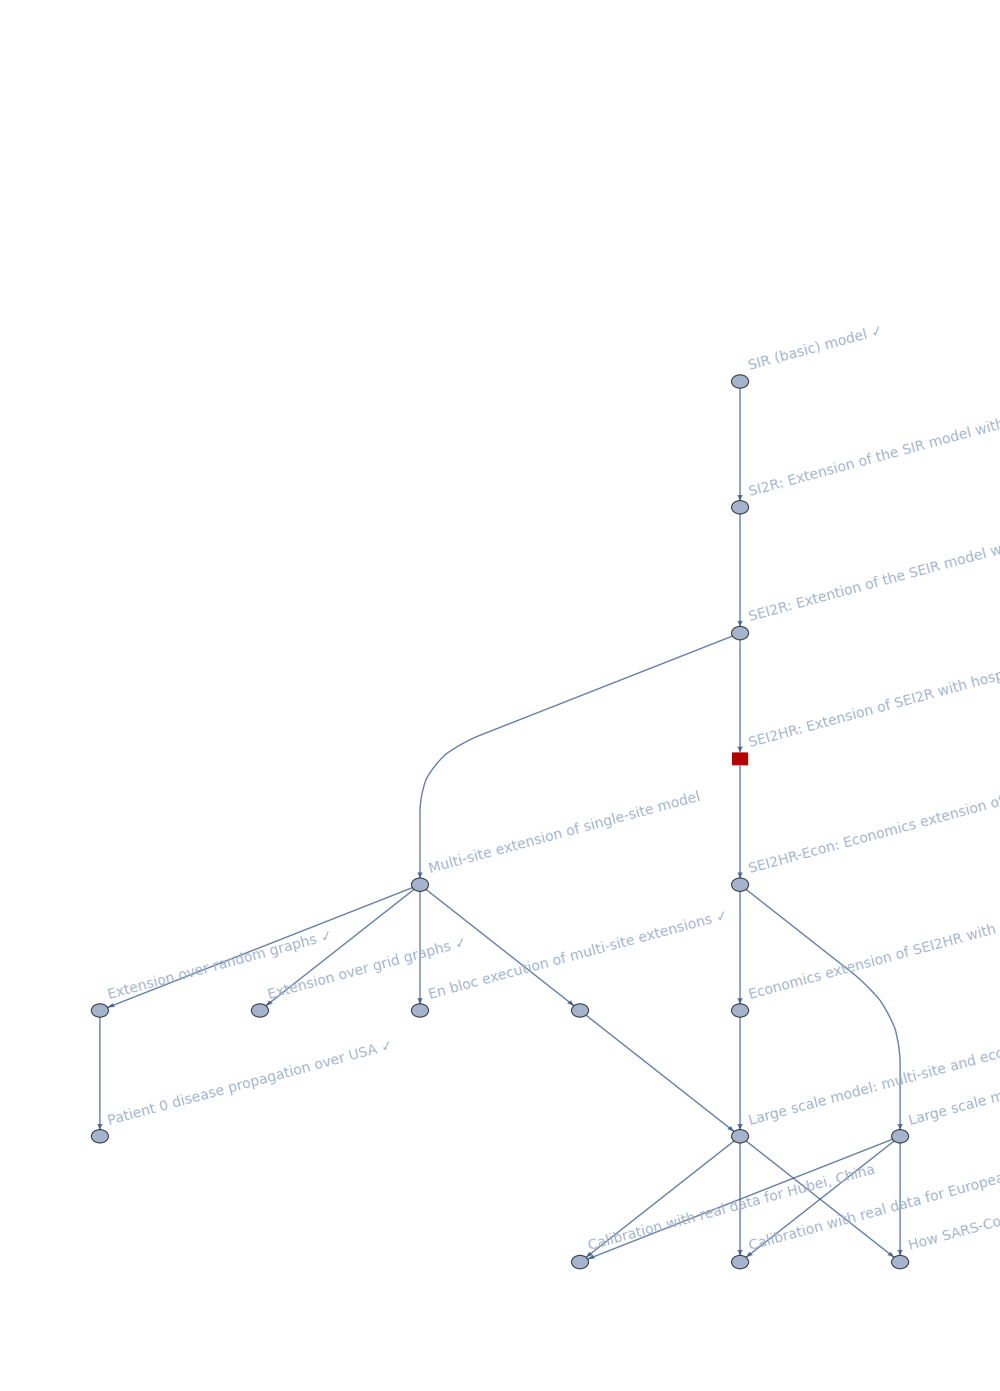

### Notebook structure

The rest of notebook has the following sequence of sections:

Package load section

SEI2HR structure in comparison of SEI2R

Explanations of the equations of SEI2HR

Quarantine scenario modeling preparation

Parameters and initial conditions setup

Populations, hospital beds, quarantine scenarios

Parametric simulation solution

Interactive interface

Sensitivity analysis

## Load paclet

The epidemiological models framework used in this notebook was originally implemented with the packages [AAp1, AAp2, AA3]; many of the plot functions are from the package [AAp4]. All those packages are included in the paclet "AntonAntonov`EpidemiologicalModeling`".

Load the paclet

```mathematica
Needs["AntonAntonov`EpidemiologicalModeling`"]
```

## SEI2HR extends SEI2R

The model SEI2HR is an extension of the model SEI2R, [AA2].

Here is SEI2R:

```mathematica
reprTP="AlgebraicEquation";
lsModelOpts={"Tooltips"->True,TooltipStyle->{Background->Yellow,CellFrameColor->Gray,FontSize->20}};
modelSEI2R=SEI2RModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelSEI2R,lsModelOpts]
```

<|Stocks→# | Symbol | Description
1 | TP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | INSP[t] | Infected Normally Symptomatic Population
5 | ISSP[t] | Infected Severely Symptomatic Population
6 | RP[t] | Recovered Population
7 | MLP[t] | Money of Lost Productivity,Rates→# | Symbol | Description
1 | μ[TP] | Population death rate
2 | μ[INSP] | Infected Normally Symptomatic Population death rate
3 | μ[ISSP] | Infected Severely Symptomatic Population death rate
4 | sspf[SP] | Severely Symptomatic Population Fraction
5 | β[INSP] | Contact rate for the infected normally symptomatic population
6 | β[ISSP] | Contact rate for the infected severely symptomatic population
7 | aip | Average infectious period
8 | aincp | Average incubation period
9 | lpcr[ISSP,INSP] | Lost productivity cost rate (per person per day),Equations→# | Equation
1 | SP'[t]==-(INSP[t] SP[t] β[INSP])/TP[t]-(ISSP[t] SP[t] β[ISSP])/TP[t]-SP[t] μ[TP]
2 | EP'[t]==(INSP[t] SP[t] β[INSP])/TP[t]+(ISSP[t] SP[t] β[ISSP])/TP[t]-EP[t] (1/aincp+μ[TP])
3 | INSP'[t]==-INSP[t]/aip+(EP[t] (1-sspf[SP]))/aincp-INSP[t] μ[INSP]
4 | ISSP'[t]==-ISSP[t]/aip+(EP[t] sspf[SP])/aincp-ISSP[t] μ[ISSP]
5 | RP'[t]==(INSP[t]+ISSP[t])/aip-RP[t] μ[TP]
6 | MLP'[t]==lpcr[ISSP,INSP] (-RP[t]-SP[t]+TP[t])
7 | TP[t]==Max[0,EP[t]+INSP[t]+ISSP[t]+RP[t]+SP[t]],RateRules→# | Symbol | Value
1 | μ[TP] | 1/45625
2 | μ[ISSP] | 0.035/aip
3 | μ[INSP] | 0.01/aip
4 | β[ISSP] | 0.15
5 | β[INSP] | 0.15
6 | aip | 26
7 | aincp | 6
8 | sspf[SP] | 0.2
9 | lpcr[ISSP,INSP] | 1,InitialConditions→# | Equation
1 | SP[0]==99998
2 | EP[0]==0
3 | ISSP[0]==1
4 | INSP[0]==1
5 | RP[0]==0
6 | MLP[0]==0
7 | TP[0]==100000|>

Here is SEI2HR:

```mathematica
modelSEI2HR=SEI2HRModel[t,"InitialConditions"->True,"RateRules"->True,"TotalPopulationRepresentation"->reprTP];
ModelGridTableForm[modelSEI2HR,lsModelOpts]
```

<|Stocks→# | Symbol | Description
1 | TP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | INSP[t] | Infected Normally Symptomatic Population
5 | ISSP[t] | Infected Severely Symptomatic Population
6 | RP[t] | Recovered Population
7 | MLP[t] | Money of Lost Productivity
8 | HP[t] | Hospitalized Population
9 | DIP[t] | Deceased Infected Population
10 | HB[t] | Hospital Beds
11 | MHS[t] | Money for Hospital Services,Rates→# | Symbol | Description
1 | μ[TP] | Population death rate
2 | μ[INSP] | Infected Normally Symptomatic Population death rate
3 | μ[ISSP] | Infected Severely Symptomatic Population death rate
4 | sspf[SP] | Severely Symptomatic Population Fraction
5 | β[INSP] | Contact rate for the infected normally symptomatic population
6 | β[ISSP] | Contact rate for the infected severely symptomatic population
7 | aip | Average infectious period
8 | aincp | Average incubation period
9 | lpcr[ISSP,INSP] | Lost productivity cost rate (per person per day)
10 | μ[HP] | Hospitalized Population death rate
11 | β[HP] | Contact rate for the hospitalized population
12 | nhbr[TP] | Number of hospital beds rate
13 | hscr[ISSP,INSP] | Hospital services cost rate (per bed per day)
14 | nhbcr[ISSP,INSP] | Number of hospital beds change rate (per day),Equations→# | Equation
1 | TP[t]==Max[0,EP[t]+INSP[t]+ISSP[t]+RP[t]+SP[t]]
2 | SP'[t]==-(HP[t] SP[t] β[HP])/TP[t]-(INSP[t] SP[t] β[INSP])/TP[t]-(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-SP[t] μ[TP]
3 | EP'[t]==(HP[t] SP[t] β[HP])/TP[t]+(INSP[t] SP[t] β[INSP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-EP[t] (1/aincp+μ[TP])
4 | INSP'[t]==-INSP[t]/aip+(EP[t] (1-sspf[SP]))/aincp-INSP[t] μ[INSP]
5 | ISSP'[t]==-ISSP[t]/aip+(EP[t] sspf[SP])/aincp-HP[t] μ[HP]-(-HP[t]+ISSP[t]) μ[ISSP]
6 | HP'[t]==(Piecewise[{{Min[HB[t]-HP[t],(EP[t] sspf[SP])/aincp], HP[t]<HB[t]}, {0, True}}])-HP[t]/aip-HP[t] μ[HP]
7 | RP'[t]==(INSP[t]+ISSP[t])/aip-RP[t] μ[TP]
8 | DIP'[t]==HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP]
9 | HB'[t]==HB[t] nhbcr[ISSP,INSP]
10 | MHS'[t]==HP[t] hscr[ISSP,INSP]
11 | MLP'[t]==lpcr[ISSP,INSP] (INSP[t]+ISSP[t]+HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP]),RateRules→# | Symbol | Value
1 | μ[TP] | 1/45625
2 | μ[ISSP] | 0.035/aip
3 | μ[INSP] | 0.01/aip
4 | β[ISSP] | 0.15
5 | β[INSP] | 0.15
6 | aip | 26
7 | aincp | 6
8 | sspf[SP] | 0.2
9 | lpcr[ISSP,INSP] | 1
10 | μ[HP] | 0.25 μ[ISSP]
11 | β[HP] | 0.1 β[ISSP]
12 | nhbr[TP] | 0.0029
13 | nhbcr[ISSP,INSP] | 0
14 | hscr[ISSP,INSP] | 1,InitialConditions→# | Equation
1 | SP[0]==99998
2 | EP[0]==0
3 | ISSP[0]==1
4 | INSP[0]==1
5 | RP[0]==0
6 | MLP[0]==0
7 | TP[0]==100000
8 | HP[0]==0
9 | DIP[0]==0
10 | HB[0]==nhbr[TP] TP[0]
11 | MHS[0]==0|>

Here are the “differences” between the two models:

```mathematica
ModelGridTableForm@Merge[{modelSEI2HR,modelSEI2R},If[AssociationQ[#⟦1⟧],KeyComplement[#],Complement@@#]&]
```

<|Stocks→# | Symbol | Description
1 | HP[t] | Hospitalized Population
2 | DIP[t] | Deceased Infected Population
3 | HB[t] | Hospital Beds
4 | MHS[t] | Money for Hospital Services,Rates→# | Symbol | Description
1 | μ[HP] | Hospitalized Population death rate
2 | β[HP] | Contact rate for the hospitalized population
3 | nhbr[TP] | Number of hospital beds rate
4 | hscr[ISSP,INSP] | Hospital services cost rate (per bed per day)
5 | nhbcr[ISSP,INSP] | Number of hospital beds change rate (per day),Equations→# | Equation
1 | DIP'[t]==HP[t] μ[HP]+INSP[t] μ[INSP]+(ISSP[t]-HP[t]) μ[ISSP]
2 | EP'[t]==(SP[t] HP[t] β[HP])/TP[t]+(INSP[t] SP[t] β[INSP])/TP[t]+(Max[0,ISSP[t]-HP[t]] SP[t] β[ISSP])/TP[t]-EP[t] (1/aincp+μ[TP])
3 | HB'[t]==HB[t] nhbcr[ISSP,INSP]
4 | HP'[t]==(Piecewise[{{Min[(EP[t] sspf[SP])/aincp,HB[t]-HP[t]], HP[t]<HB[t]}, {0, True}}])-HP[t]/aip-HP[t] μ[HP]
5 | ISSP'[t]==-ISSP[t]/aip+(EP[t] sspf[SP])/aincp-HP[t] μ[HP]-(ISSP[t]-HP[t]) μ[ISSP]
6 | MHS'[t]==HP[t] hscr[ISSP,INSP]
7 | MLP'[t]==lpcr[ISSP,INSP] (INSP[t]+ISSP[t]+HP[t] μ[HP]+INSP[t] μ[INSP]+(ISSP[t]-HP[t]) μ[ISSP])
8 | SP'[t]==-(SP[t] HP[t] β[HP])/TP[t]-(INSP[t] SP[t] β[INSP])/TP[t]-(Max[0,ISSP[t]-HP[t]] SP[t] β[ISSP])/TP[t]-SP[t] μ[TP],RateRules→# | Symbol | Value
1 | μ[HP] | 0.25 μ[ISSP]
2 | β[HP] | 0.1 β[ISSP]
3 | nhbr[TP] | 0.0029
4 | nhbcr[ISSP,INSP] | 0
5 | hscr[ISSP,INSP] | 1,InitialConditions→# | Equation
1 | DIP[0]==0
2 | HB[0]==nhbr[TP] TP[0]
3 | HP[0]==0
4 | MHS[0]==0|>

## Equations explanations

In this section we provide rationale of the model equations of SEI2HR.

The equations for Susceptible, Exposed, Infected, Recovered populations of SEI2R are "standard" and explanations about them are found in [WK1, HH1]. For SEI2HR those equations change because of the stocks Hospitalized Population and Hospital Beds.

The equations time unit is one day. The time horizon is one year. Since we target COVID-19, [Wk2, AA1], we do not consider births.

Remark: For convenient reading the equations in this section have tooltips for the involved stocks and rates.

### Verbal description of the model

We start with one infected (normally symptomatic) person, the rest of the people are susceptible. The infected people meet other people directly or get in contact with them indirectly. (Say, susceptible people touch things touched by infected.) For each susceptible person there is a probability to get the decease. The decease has an incubation period: before becoming infected the susceptible are (merely) exposed. The infected recover after a certain average infection period or die. A certain fraction of the infected become severely symptomatic. If there are enough hospital beds the severely symptomatic infected are hospitalized. The hospitalized severely infected have different death rate than the non-hospitalized ones. The number of hospital beds might change: hospitals are extended, new hospitals are build, or there are not enough medical personnel or supplies. The deaths from infection are tracked (accumulated.) Money for hospital services and money from lost productivity are tracked (accumulated.)

The equations below give mathematical interpretation of the model description above.

### Code for the equations

Each equation in this section are derived with code like this:

```mathematica
ModelGridTableForm[modelSEI2HR, lsModelOpts]["Equations"][[1, EquationPosition[modelSEI2HR, RP] + 1, 2]]
```

and then the output cell is edited to be “DisplayFormula” and have CellLabel value corresponding to the stock of interest.

### The infected and hospitalized populations

SEI2HR has two types of infected populations: a normally symptomatic one and a severely symptomatic one. A major assumption for SEI2HR is that only the severely symptomatic people are hospitalized. (That assumption is also reflected in the diagram in the introduction.)

Each of those three populations have their own contact rates and mortality rates.

Here are the contact rates from the SEI2HR dictionary

```mathematica
ColumnForm@Cases[Normal@modelSEI2HR["Rates"],HoldPattern[β[_]->_],∞]
```

β[INSP]→Contact rate for the infected normally symptomatic population
β[ISSP]→Contact rate for the infected severely symptomatic population
β[HP]→Contact rate for the hospitalized population

Here are the mortality rates from the SEI2HR dictionary

```mathematica
ColumnForm@Cases[Normal@modelSEI2HR["Rates"],HoldPattern[μ[_]->_],∞]
```

μ[TP]→Population death rate
μ[INSP]→Infected Normally Symptomatic Population death rate
μ[ISSP]→Infected Severely Symptomatic Population death rate
μ[HP]→Hospitalized Population death rate

Remark: Below with “Infected Population” we mean both stocks Infected Normally Symptomatic Population (INSP) and Infected Severely Symptomatic Population (ISSP).

### Total Population

In this notebook we consider a DAE’s formulation of SEI2HR. The stock Total Population has the following (obvious) algebraic equation:

TP[t]==Max[0,EP[t]+INSP[t]+ISSP[t]+RP[t]+SP[t]]

Note that with Max we specified that the total population cannot be less than 0.

Remark: As mentioned in the introduction, the package [AAp1] allows for the use of non-algebraic formulation, without an equation for TP.

### Susceptible Population

The stock Susceptible Population (SP) is decreased by (1) infections derived from stocks Infected Populations and Hospitalized Population (HP), and (2) morality cases derived with the typical mortality rate.

SP'[t]==-(HP[t] SP[t] β[HP])/TP[t]-(INSP[t] SP[t] β[INSP])/TP[t]-(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-SP[t] μ[TP]

Because we hospitalize the severely infected people only instead of the term

(ISSP[t]SP[t]β[ISSP])/TP[t]

we have the terms

(HP[t] SP[t] β[HP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t].

The first term is for the infections derived from the hospitalized population. The second term for the infections derived from people who are infected severely symptomatic and not hospitalized.

#### Births term

Note that we do not consider in this notebook births, but the births term can be included in SP’s equation:

```mathematica
Block[{m=SEI2HRModel[t,"BirthsTerm"->True]},
ModelGridTableForm[m]["Equations"]⟦1,EquationPosition[m,SP]+1,2⟧
]
```

SP'[t]==-SP[t] μ[TP]-(HP[t] SP[t] β[HP])/TP[0]-(INSP[t] SP[t] β[INSP])/TP[0]-(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[0]+μ[TP] TP[0]

The births rate is the same as the death rate, but it can be programmatically changed. (See [AAp2].)

### Exposed Population

The stock Exposed Population (EP) is increased by (1) infections derived from the stocks Infected Populations and Hospitalized Population, and (2) mortality cases derived with the typical mortality rate. EP is decreased by (1) the people who after a certain average incubation period (aincp) become ill, and (2) mortality cases derived with the typical mortality rate.

EP'[t]==(HP[t] SP[t] β[HP])/TP[t]+(INSP[t] SP[t] β[INSP])/TP[t]+(Max[0,-HP[t]+ISSP[t]] SP[t] β[ISSP])/TP[t]-EP[t] (1/aincp+μ[TP])

### Infected Normally Symptomatic Population

INSP is increased by a fraction of the people who have been exposed. That fraction is derived with the parameter severely symptomatic population fraction (sspf). INSP is decreased by (1) the people who recover after a certain average infection period (aip), and (2) the normally symptomatic people who die from the disease.

INSP'[t]==-INSP[t]/aip+(EP[t] (1-sspf[SP]))/aincp-INSP[t] μ[INSP]

### Infected Severely Symptomatic Population

ISSP is increased by a fraction of the people who have been exposed. That fraction is corresponds to the parameter severely symptomatic population fraction (sspf). ISSP is decreased by (1) the people who recover after a certain average infection period (aip), (2) the hospitalized severely symptomatic people who die from the disease, and (3) the non-hospitalized severely symptomatic people who die from the disease.

ISSP'[t]==-ISSP[t]/aip+(EP[t] sspf[SP])/aincp-HP[t] μ[HP]-(-HP[t]+ISSP[t]) μ[ISSP]

Note that we do not assume that severely symptomatic people recover faster if they are hospitalized, only that they have a different death rate.

### Hospitalized Population

The amount of people that can be hospitalized is determined by the available Hospital Beds (HB) -- the stock Hospitalized Population (HP) is subject to a resource limitation by the stock HB.

The equation of the stock HP can be easily understood from the following dynamics description points:

If the number of hospitalized people is less that the number of hospital beds we hospitalize the new ISSP people.

If the new ISSP people are more than the Available Hospital Beds (AHB) we take as many as AHB.

Hospitalized people have the same average infection period (aip).

Hospitalized (severely symptomatic) people have their own mortality rate.

HP'[t]==(Piecewise[{{Min[HB[t]-HP[t],(EP[t] sspf[SP])/aincp], HP[t]<HB[t]}, {0, True}}])-HP[t]/aip-HP[t] μ[HP]

Note that although we know that in a given day some hospital beds are going to be freed they are not considered in the hospitalization plans for that day.

### Recovered Population

The stock Recovered Population (RP) is increased by the recovered infected people and decreased by mortality cases derived with the typical mortality rate.

RP'[t]==(INSP[t]+ISSP[t])/aip-RP[t] μ[TP]

### Deceased Infected Population

The stock Deceased Infected Population (DIP) accumulates the deaths of the people who are infected. Note that we utilize the different death rates for HP and ISSP.

DIP'[t]==HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP]

### Hospital Beds

The stock Hospital Beds (HB) can change with a rate that reflects the number of hospital beds change rate (nhbcr) per day. Generally speaking, using nhbcr we can capture scenarios, like, extending hospitals, building new hospitals, recruitment of new medical personnel, loss of medical personnel (due to infections.)

HB'[t]==HB[t] nhbcr[ISSP,INSP]

### Money for Hospital Services

The stock Money for Hospital Services (MHS) simply tracks expenses for hospitalized people. The parameter hospital services cost rate (hscr) with unit money per bed per day simply multiplies HP.

MHS'[t]==HP[t] hscr[ISSP,INSP]

### Money from Lost Productivity

The stock Money from Lost Productivity (MLP) simply tracks the work non-availability of the infected and died from infection people. The parameter lost productivity cost rate (lpcr) with unit money per person per day multiplies the total count of the infected and dead from infection.

MLP'[t]==lpcr[ISSP,INSP] (INSP[t]+ISSP[t]+HP[t] μ[HP]+INSP[t] μ[INSP]+(-HP[t]+ISSP[t]) μ[ISSP])

## Quarantine scenarios

In order to model quarantine scenarios we use piecewise constant functions for the contact rates β[ISSP] and β[INSP].

Remark: Other functions can be used, like, functions derived through some statistical fitting.

Here is an example plot :

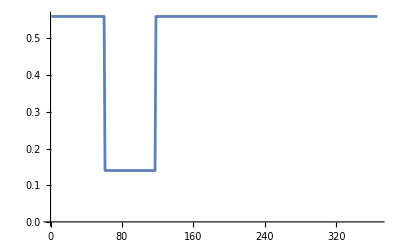

```mathematica
Block[{func=β*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1]},
Legended[
Block[{β=0.56,qsd=60,ql=8*7,qcrf=0.25},
ListLinePlot[Table[func,{t,0,365}],PlotStyle->"Detailed"]
],func]]
```

To model quarantine with a piecewise constant function we use the following  parameters:

qsd for quarantine's start

ql for quarantines duration

qcrf for the effect on the quarantine on the contact rate

## Parameters and actual simulation equations code

Here are the parameters we want to experiment with (or do calibration with):

```mathematica
lsFocusParams={aincp,aip,sspf[SP],β[HP],qsd,ql,qcrf,nhbcr[ISSP,INSP],nhbr[TP]};
```

Here we set custom rates and initial conditions:

```mathematica
population=10^6;
If[reprTP=="AlgebraicEquation",
modelSEI2HR=SetRateRules[modelSEI2HR,
<|
β[ISSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
β[INSP]->0.5*Piecewise[{{1,t<qsd},{qcrf,qsd≤t≤qsd+ql}},1],
qsd->60,
ql->8*7,
qcrf->0.25,
β[HP]->0.01,
μ[ISSP]->0.035/aip,
μ[INSP]->0.01/aip,
nhbr[TP]->3/1000,
lpcr[ISSP,INSP]->1,
hscr[ISSP,INSP]->1
|>];
modelSEI2HR=SetInitialConditions[modelSEI2HR,<|TP[0]->population,SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>],
(*ELSE*)
modelSEI2HR=SetRateRules[modelSEI2HR,<|TP[t]->population,β[ISSP]->0.56,β[INSP]->0.56,β[HP]->0.01,μ[ISSP]->0.035/aip,μ[INSP]->0.01/aip,μ[HP]->0.005/aip,nhbr[TP]->population*3/1000|>];modelSEI2HR=SetInitialConditions[modelSEI2HR,<|SP[0]->population-1,ISSP[0]->0,INSP[0]->1|>];
];
```

Remark: Note the piecewise functions for β[ISSP] and β[INSP].

Here is the system of ODE’s we use to do parametrized simulations:

```mathematica
lsActualEquations=
Join[
modelSEI2HR["Equations"]//.KeyDrop[modelSEI2HR["RateRules"],lsFocusParams],
modelSEI2HR["InitialConditions"]//.KeyDrop[modelSEI2HR["RateRules"],lsFocusParams]
];
ResourceFunction["GridTableForm"][List/@lsActualEquations]
```

# | 1
1 | TP[t]==Max[0,EP[t]+INSP[t]+ISSP[t]+RP[t]+SP[t]]
2 | SP'[t]==-SP[t]/45625-(0.5 INSP[t] (Piecewise[{{1, t<qsd}, {qcrf, qsd≤t≤ql+qsd}, {1, True}}]) SP[t])/TP[t]-(0.5 Max[0,-HP[t]+ISSP[t]] (Piecewise[{{1, t<qsd}, {qcrf, qsd≤t≤ql+qsd}, {1, True}}]) SP[t])/TP[t]-(HP[t] SP[t] β[HP])/TP[t]
3 | EP'[t]==-((1/45625+1/aincp) EP[t])+(0.5 INSP[t] (Piecewise[{{1, t<qsd}, {qcrf, qsd≤t≤ql+qsd}, {1, True}}]) SP[t])/TP[t]+(0.5 Max[0,-HP[t]+ISSP[t]] (Piecewise[{{1, t<qsd}, {qcrf, qsd≤t≤ql+qsd}, {1, True}}]) SP[t])/TP[t]+(HP[t] SP[t] β[HP])/TP[t]
4 | INSP'[t]==-(1.01 INSP[t])/aip+(EP[t] (1-sspf[SP]))/aincp
5 | ISSP'[t]==-(0.00875 HP[t])/aip-ISSP[t]/aip-(0.035 (-HP[t]+ISSP[t]))/aip+(EP[t] sspf[SP])/aincp
6 | HP'[t]==-(1.00875 HP[t])/aip+(Piecewise[{{Min[HB[t]-HP[t],(EP[t] sspf[SP])/aincp], HP[t]<HB[t]}, {0, True}}])
7 | RP'[t]==(INSP[t]+ISSP[t])/aip-RP[t]/45625
8 | DIP'[t]==(0.00875 HP[t])/aip+(0.01 INSP[t])/aip+(0.035 (-HP[t]+ISSP[t]))/aip
9 | HB'[t]==HB[t] nhbcr[ISSP,INSP]
10 | MHS'[t]==HP[t]
11 | MLP'[t]==(0.00875 HP[t])/aip+INSP[t]+(0.01 INSP[t])/aip+ISSP[t]+(0.035 (-HP[t]+ISSP[t]))/aip
12 | SP[0]==999999
13 | EP[0]==0
14 | ISSP[0]==0
15 | INSP[0]==1
16 | RP[0]==0
17 | MLP[0]==0
18 | TP[0]==1000000
19 | HP[0]==0
20 | DIP[0]==0
21 | HB[0]==nhbr[TP] TP[0]
22 | MHS[0]==0

## Simulation

### Solutions

Straightforward simulation for one year using ParametricNDSolve :

```mathematica
aSol=
Association@Flatten@
ParametricNDSolve[lsActualEquations,GetStockSymbols[modelSEI2HR,__~~__],{t,0,365},lsFocusParams];
```

### Example evaluation

Here are the parameters of a stock solution:

```mathematica
aSol[HP]["Parameters"]
```

{aincp,aip,sspf[SP],β[HP],qsd,ql,qcrf,nhbcr[ISSP,INSP],nhbr[TP]}

Here we replace the parameters with concrete rate values (kept in the model object):

```mathematica
aSol[HP]["Parameters"]//.modelSEI2HR["RateRules"]
```

{6,26,0.2,0.01,60,56,0.25,0,3/1000}

Here is an example evaluation of a solution using the parameter values above:

```mathematica
With[{seq=Sequence@@(aSol[HP]["Parameters"]//.modelSEI2HR["RateRules"])},aSol[HP][seq][100]]
```

2887.95

## Interactive interface

Using the interface in this section we can interactively see the effects of changing the focus parameters.

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->400};
lsPopulationKeys={TP,SP,EP,ISSP,INSP,HP,RP,DIP,HB};
lsEconKeys={MHS,MLP};
Manipulate[
DynamicModule[{aStocks=modelSEI2HR["Stocks"],aSolLocal=aSol,lsPopulationPlots,lsEconPlots,lsRestPlots},

lsPopulationPlots=
ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsPopulationKeys,displayStocks]],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->popLogPlotQ,"Together"->popTogetherQ,"Derivatives"->popDerivativesQ,"DerivativePrefix"->"Δ",opts];

lsEconPlots=
ParametricSolutionsPlots[
aStocks,
KeyTake[aSolLocal,Intersection[lsEconKeys,displayStocks]],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->econLogPlotQ,"Together"->econTogetherQ,"Derivatives"->econDerivativesQ,"DerivativePrefix"->"Δ",opts];

lsRestPlots=
If[Length[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsEconKeys]]]==0,{},
(*ELSE*)
ParametricSolutionsPlots[
aStocks,
KeyTake[KeyDrop[aSolLocal,Join[lsPopulationKeys,lsEconKeys]],displayStocks],
{aincp,aip,spf,crhp,qsd,ql,qcrf,nhbcr,nhbr/1000},ndays,
"LogPlot"->econLogPlotQ,"Together"->econTogetherQ,"Derivatives"->econDerivativesQ,"DerivativePrefix"->"Δ",opts]
];

Multicolumn[Join[lsPopulationPlots,lsEconPlots,lsRestPlots],nPlotColumns,Dividers->All,FrameStyle->GrayLevel[0.8]],
SaveDefinitions->True
],
{{displayStocks,Join[lsPopulationKeys,lsEconKeys],"Stocks to display:"},Join[lsPopulationKeys,lsEconKeys],ControlType->TogglerBar},
{{aincp,6.,"Average incubation period (days)"},1,60.,1,Appearance->{"Open"}},
{{aip,21.,"Average infectious period (days)"},1,60.,1,Appearance->{"Open"}},
{{spf,0.2,"Severely symptomatic population fraction"},0,1,0.025,Appearance->{"Open"}},
{{qsd,65,"Quarantine start days"},0,365,0.01,Appearance->{"Open"}},
{{ql,8*7,"Quarantine length (in days)"},0,120,1,Appearance->{"Open"}},
{{qcrf,0.25,"Quarantine contact rate fraction"},0,1,0.01,Appearance->{"Open"}},
{{crhp,0.1,"Contact rate of the hospitalized population"},0,30,0.1,Appearance->{"Open"}},
{{nhbcr,0,"Number of hospital beds change rate"},-0.5,0.5,0.001,Appearance->{"Open"}},
{{nhbr,2.9,"Number of hospital beds rate (per 1000 people)"},0,100,0.1,Appearance->{"Open"}},
{{ndays,365,"Number of days"},1,365,1,Appearance->{"Open"}},
{{popTogetherQ,True,"Plot populations together"},{False,True}},
{{popDerivativesQ,False,"Plot populations derivatives"},{False,True}},
{{popLogPlotQ,False,"LogPlot populations"},{False,True}},
{{econTogetherQ,True,"Plot economics functions together"},{False,True}},
{{econDerivativesQ,False,"Plot economics functions derivatives"},{False,True}},
{{econLogPlotQ,True,"LogPlot economics functions"},{False,True}},
{{nPlotColumns,1,"Number of plot columns"},Range[5]},
ControlPlacement->Left,ContinuousAction->False]
```

## Sensitivity analysis

When making and using this kind of dynamics models it is important to see how the solutions react to changes of different parameters. For example, we should try to find answers to questions like "What ranges of which parameters bring dramatic changes into important stocks?"

Sensitivity analysis is used to determine how sensitive is a SD model to changes of the parameters and to changes of model’s equations, [BC1]. More specifically, parameter sensitivity, which we apply below, allows us to see the changes of stocks dynamic behaviour for different sequences (and combinations) of parameter values.

Remark: The sensitivity analysis shown below should be done for other stocks and rates. In order to keep this exposition short we focus on ISSP, DIP, and HP.

It is interesting to think in terms of “3D parameter sensitivity plots.” We also do such plots.

### Evaluations by Area under the curve

For certain stocks we might be not just interested in their evolution in time but also in their cumulative values. I.e. we are interested in the so called Area Under the Curve (AUC) metric for those stocks.

There are three ways to calculate AUC for stocks of interest:

Add aggregation equations in the system of ODE’s. (Similar to the stock DIP in SEI2HR.)

For example, in order to compute AUC for ISSP we can add to SEI2HR the equation:

aucISSP'[t]=ISSP[t]

More details for such equation addition are given in [AA2].

Apply NIntegrate over stocks solution functions.

Apply Trapezoidal rule to stock solution function values over a certain time grid.

Below we use 1 and 3.

Remark: The AUC measure for a stock is indicated with the prefix “∫”. For example AUC for ISSP is marked with “∫ISSP”.

### Ranges

Below we use the following sets of quarantine starts and quarantine durations.

```mathematica
lsQStartRange=Join[{365},Range[50,100,5],{140}];
lsQLengthRange=Join[{0},Range[2*7,12*7,7]];
```

Note that putting the quarantine start to be at day 365 means “no quarantine.”

### Number of infected people

#### Quarantine starts sensitivity

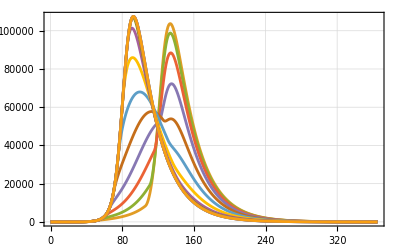
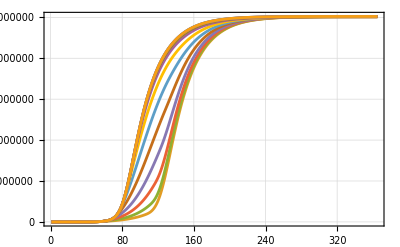
# | ISSP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 2.93 | 0.
2 | 50 | 14.52 | -11.59
3 | 55 | 13.97 | -11.04
4 | 60 | 13.04 | -10.11
5 | 65 | 11.68 | -8.74
6 | 70 | 10.2 | -7.27
7 | 75 | 9.31 | -6.38
8 | 80 | 8.13 | -5.2
9 | 85 | 5.78 | -2.84
10 | 90 | 4.05 | -1.12
11 | 95 | 3.34 | -0.41
12 | 100 | 3.09 | -0.16
13 | 140 | 2.93 | 0.ISSPwrtqsd
# | ∫ISSP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 5.02186×10^6 | 0.
2 | 50 | 5.01964×10^6 | 2229.42
3 | 55 | 5.02043×10^6 | 1436.64
4 | 60 | 5.02101×10^6 | 855.87
5 | 65 | 5.02163×10^6 | 236.23
6 | 70 | 5.02139×10^6 | 475.38
7 | 75 | 5.01724×10^6 | 4626.44
8 | 80 | 5.01047×10^6 | 11397.3
9 | 85 | 5.01094×10^6 | 10923.2
10 | 90 | 5.01573×10^6 | 6139.62
11 | 95 | 5.01907×10^6 | 2797.09
12 | 100 | 5.0206×10^6 | 1265.25
13 | 140 | 5.02184×10^6 | 24.8ISSPwrtqsd

```mathematica
ColumnForm[Map[StockVariabilityPlot[aSol,ISSP,Join[modelSEI2HR["RateRules"],<|ql->8*7|>],{qsd,lsQStartRange},365,"Operation"->#,opts,ImageSize->300]&,{"Identity","Integral"}]]
```

Note that the plots and tabulated differences with “no quarantine” indicate that there is a very narrow range to choose an effective quarantine start.

#### Quarantine duration sensitivity

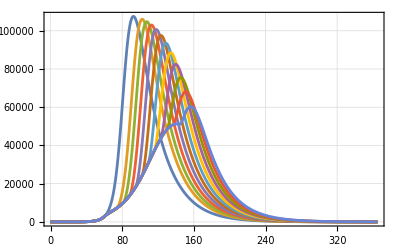
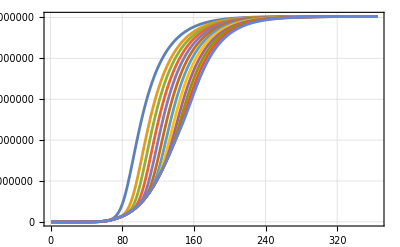
# | ISSP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 0 | 2.93 | 0.
2 | 14 | 4.27 | -1.34
3 | 21 | 5.19 | -2.26
4 | 28 | 6.3 | -3.37
5 | 35 | 7.61 | -4.68
6 | 42 | 9.16 | -6.23
7 | 49 | 10.97 | -8.04
8 | 56 | 13.04 | -10.11
9 | 63 | 15.39 | -12.45
10 | 70 | 18.04 | -15.11
11 | 77 | 21.07 | -18.14
12 | 84 | 24.64 | -21.71ISSPwrtql
# | ∫ISSP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 0 | 5.02186×10^6 | 0.
2 | 14 | 5.02154×10^6 | 320.9
3 | 21 | 5.02139×10^6 | 472.73
4 | 28 | 5.02126×10^6 | 607.25
5 | 35 | 5.02115×10^6 | 718.58
6 | 42 | 5.02106×10^6 | 800.38
7 | 49 | 5.02102×10^6 | 846.92
8 | 56 | 5.02101×10^6 | 855.87
9 | 63 | 5.02103×10^6 | 833.51
10 | 70 | 5.02106×10^6 | 804.64
11 | 77 | 5.02103×10^6 | 830.49
12 | 84 | 5.02083×10^6 | 1037.17ISSPwrtql

```mathematica
ColumnForm[Map[StockVariabilityPlot[aSol,ISSP,Join[modelSEI2HR["RateRules"],<|qsd->60|>],{ql,lsQLengthRange},365,"Operation"->#,opts,ImageSize->300]&,{"Identity","Integral"}]]
```

### Number of deceased people

#### Quarantine starts sensitivity

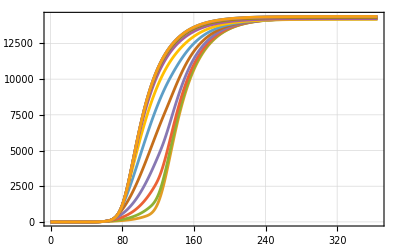
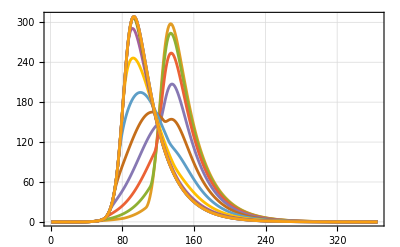
# | DIP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 14391.6 | 0.
2 | 50 | 14287.1 | 104.54
3 | 55 | 14266.5 | 125.12
4 | 60 | 14260.9 | 130.68
5 | 65 | 14254.9 | 136.72
6 | 70 | 14239.2 | 152.44
7 | 75 | 14210.1 | 181.47
8 | 80 | 14192.2 | 199.4
9 | 85 | 14236.4 | 155.21
10 | 90 | 14323.3 | 68.33
11 | 95 | 14366.9 | 24.7
12 | 100 | 14383.2 | 8.39
13 | 140 | 14391.6 | 0.05DIPwrtqsd
# | ΔDIP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 0.01 | 0.
2 | 50 | 0.05 | -0.04
3 | 55 | 0.04 | -0.04
4 | 60 | 0.04 | -0.03
5 | 65 | 0.04 | -0.03
6 | 70 | 0.03 | -0.02
7 | 75 | 0.03 | -0.02
8 | 80 | 0.02 | -0.01
9 | 85 | 0.02 | -0.01
10 | 90 | 0.01 | 0.
11 | 95 | 0.01 | 0.
12 | 100 | 0.01 | 0.
13 | 140 | 0.01 | 0.DIPwrtqsd

```mathematica
ColumnForm[Map[StockVariabilityPlot[aSol,DIP,Join[modelSEI2HR["RateRules"],<|ql->8*7|>],{qsd,lsQStartRange},365,"Operation"->#,opts,ImageSize->300]&,{"Identity","Derivative"}]]
```

### Number of hospitalized people

#### Quarantine starts sensitivity

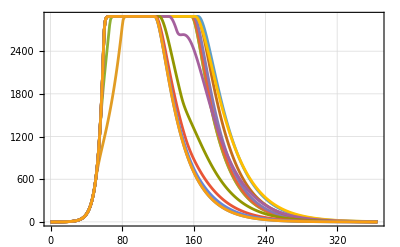
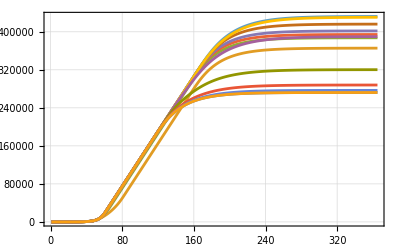
# | HP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 0.25 | 0.
2 | 50 | 1.22 | -0.97
3 | 55 | 1.24 | -0.99
4 | 60 | 1.3 | -1.06
5 | 65 | 1.53 | -1.29
6 | 70 | 2.24 | -1.99
7 | 75 | 3.7 | -3.45
8 | 80 | 4.48 | -4.23
9 | 85 | 3.04 | -2.79
10 | 90 | 1.4 | -1.15
11 | 95 | 0.68 | -0.43
12 | 100 | 0.42 | -0.17
13 | 140 | 0.25 | 0.HPwrtqsd
# | ∫HP | Differences at 365
1 | -Graphics- | # | Parameter | End values | Difference
with the first
1 | 365 | 272260. | 0.
2 | 50 | 365560. | -93300.3
3 | 55 | 387379. | -115119.
4 | 60 | 394297. | -122037.
5 | 65 | 401791. | -129531.
6 | 70 | 416123. | -143862.
7 | 75 | 432248. | -159988.
8 | 80 | 430494. | -158233.
9 | 85 | 389714. | -117454.
10 | 90 | 320269. | -48008.4
11 | 95 | 288004. | -15744.
12 | 100 | 276733. | -4473.22
13 | 140 | 272235. | 24.8HPwrtqsd

```mathematica
ColumnForm[Map[StockVariabilityPlot[aSol,HP,Join[modelSEI2HR["RateRules"],<|ql->8*7|>],{qsd,lsQStartRange},365,"Operation"->#,opts,ImageSize->300]&,{"Identity","Integral"}]]
```

### Infected Severely Symptomatic Population stock integral with respect to quarantine start and length

In this section the 3D plot of AUC of ISSP is calculated using Trapezoidal rule.

```mathematica
AbsoluteTiming[
aVals=Association@Flatten@Table[{qsdVar,qlVar}->ParametricFunctionValues[aSol[ISSP],Join[modelSEI2HR["RateRules"],<|qsd->qsdVar,ql->qlVar|>],{0,365,1}],{qsdVar,50,120,5},{qlVar,10,120,5}];
]
```

{8.08863,Null}

```mathematica
ListPlot3D[KeyValueMap[Append[#1,#2]&,TrapezoidalRule/@aVals],AxesLabel->{"Quaratine start","Quarantine length","Infected Severely Symptomatic Population AUC"},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

### Deceased Infected Population stock with respect to quarantine start and length

We can see from SEI2HR’s equations that DIP is already an AUC type of value. We can just plot the DIP values at the time horizon (one year.)

```mathematica
focusStock=DIP;
```

```mathematica
AbsoluteTiming[
aVals=Association@Flatten@Table[{qsdVar,qlVar}->ParametricFunctionValues[aSol[focusStock],Join[modelSEI2HR["RateRules"],<|qsd->qsdVar,ql->qlVar|>],{365,365,1}],{qsdVar,50,120,5},{qlVar,2*7,12*7,7}];
]
```

{3.41557,Null}

```mathematica
ListPlot3D[KeyValueMap[Join[#1,#2⟦1,{2}⟧]&,aVals],AxesLabel->{"Quarantine start","Quarantine duration",focusStock[t]/.modelSEI2HR["Stocks"]},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

### Hospitalized Population stock integral with respect to quarantine start and length

In this section the 3D plot of AUC of HP is calculated using Trapezoidal rule.

```mathematica
AbsoluteTiming[
aVals=Association@Flatten@Table[{qsdVar,qlVar}->ParametricFunctionValues[aSol[HP],Join[modelSEI2HR["RateRules"],<|qsd->qsdVar,ql->qlVar|>],{0,365,1}],{qsdVar,50,120,5},{qlVar,10,120,5}];
]
```

{7.50505,Null}

```mathematica
ListPlot3D[KeyValueMap[Append[#1,#2]&,TrapezoidalRule/@aVals],AxesLabel->{"Quaratine start","Quarantine length","Hospitalized population AUC"},PlotRange->All,ImageSize->Large]
```

-Graphics3D-

## References

### Articles

[Wk1] Wikipedia entry, "Compartmental models in epidemiology".

[Wl2] Wikipedia entry, "Coronavirus disease 2019".

[HH1] Herbert W. Hethcote (2000). "The Mathematics of Infectious Diseases". SIAM Review. 42 (4): 599–653. Bibcode:2000SIAMR..42..599H. doi:10.1137/s0036144500371907.

[BC1] Lucia Breierova,  Mark Choudhari,  An Introduction to Sensitivity Analysis, (1996), Massachusetts Institute of Technology.

[AA1] Anton Antonov, "Coronavirus propagation modeling considerations", (2020), SystemModeling at GitHub.

[AA2] Anton Antonov, "Basic experiments workflow for simple epidemiological models", (2020), SystemModeling at GitHub.

[AA3] Anton Antonov, "Scaling of Epidemiology Models with Multi-site Compartments", (2020), SystemModeling at GitHub.

### Repositories, packages

[WRI1] Wolfram Research, Inc., "Epidemic Data for Novel Coronavirus COVID-19", WolframCloud.

[AAr1] Anton Antonov, Coronavirus propagation dynamics project, (2020), SystemModeling at GitHub.

[AAp1] Anton Antonov, "Epidemiology models Mathematica package", (2020), SystemsModeling at GitHub.

[AAp2] Anton Antonov, "Epidemiology models modifications Mathematica package", (2020), SystemsModeling at GitHub.

[AAp3] Anton Antonov, "Epidemiology modeling visualization functions Mathematica package", (2020), SystemsModeling at GitHub.

[AAp4] Anton Antonov, "System dynamics interactive interfaces functions Mathematica package", (2020), SystemsModeling at GitHub.

### Project management files

[AAo1] Anton Antonov, WirVsVirus-Hackathon-work-plan.org, (2020), SystemsModeling at GitHub.

[AAo2] Anton Antonov, WirVsVirus-hackathon-Geo-spatial-temporal-model-mind-map, (2020), SystemsModeling at GitHub.

Related Guides

Epidemiological modeling

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/EpidemiologicalModeling

AntonAntonov`EpidemiologicalModeling`

AntonAntonov/EpidemiologicalModeling/tutorial/SEI2HRmodelwithquarantinescenarios

### Keywords